```mathematica
mecSquared = 0.511*10^6;
hbarC = 197.33 * 10^6*10^(-15);
e0 = -13.6;
e0Abs = Abs[e0];
a0 = 0.529*10^(-10);
```

```mathematica
kappaSquared = (2*mecSquared/(hbarC)^2)*e0Abs
```

3.56947×10^20

```mathematica
kSquared[v_] := (2*mecSquared/(hbarC)^2)*(v-e0Abs);
z0Squared[v_]:= (2*mecSquared/(hbarC)^2)*a0^2*v;
eta[v_]:= Sqrt[kSquared[v]]*a0;
xi:=Sqrt[kappaSquared]*a0;
```

{}

```mathematica
FindRoot[{xi-eta[v]*Tan[eta[v]]==0}, {v, 0, 400}]
```

{v→23.6735}

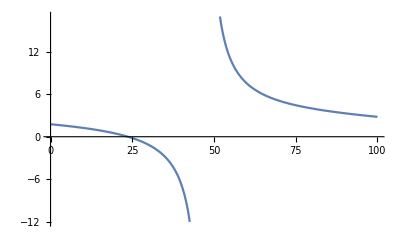

```mathematica
Plot[xi-eta[v]*Tan[eta[v]], {v,0, 100}]
```

```mathematica
v0=23.67
xi-eta[v0]*Tan[eta[v0]]
```

23.67

0.000476626

```mathematica
Sqrt[z0Squared[23]]
```

1.29973

```mathematica
Sqrt[eta[23]^2+xi^2]
```

1.02376

```mathematica
v0 = 23.67;
kappaSquaredE[e_] := (2*mecSquared/(hbarC)^2)*Abs[e];
kSquaredE[e_] := (2*mecSquared/(hbarC)^2)*(v0-Abs[e]);
z0SquaredE:= (2*mecSquared/(hbarC)^2)*a0^2*v0;
etaE[e_]:= Sqrt[kSquaredE[e]]*a0;
xiE[e_]:=Sqrt[kappaSquaredE[e]]*a0;
```

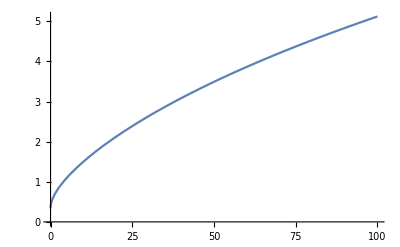

```mathematica
Plot[xiE[e]+etaE[e]*Cot[etaE[e]], {e,0, 100}]
```

```mathematica
FindRoot[{xiE[e]-etaE[e]*Tan[etaE[e]]==0}, {e, 400}]
```

{e→13.5972+0. ⅈ}